## Atomic to Physical Unit Conversions

```mathematica
(* 1 GHz below ZFIP in AU *)
enAU=Quantity[4.35974417*10^-18,"Joules"];
enAU1GHz=UnitConvert[Quantity["PlanckConstant"]*Quantity[1,"Gigahertz"]/enAU];
Print["1 GHz Photon Energy = ",enAU1GHz, " A.U."]
(* 1 ns in AU *)
tAU=Quantity[2.418884326505*10^-17,"Seconds"];
tAU1ns=UnitConvert[Quantity[1,"nanosecond"]/tAU];
Print["1 ns = ",tAU1ns, " A.U."]
(* 1 mV/cm in AU *)
fAU=Quantity[5.14220652*10^11,"Volts"/"Meters"];
fAU1mVcm=UnitConvert[Quantity[1,"Millivolts"/"Centimeters"]/fAU];
Print["1 mV/cm = ",fAU1mVcm," A.U."]
```

1 GHz Photon Energy = 1.51983×10^-7 A.U.

1 ns = 4.13414×10^7 A.U.

1 mV/cm = 1.94469×10^-13 A.U.

## Inner Turning Point Integral

```mathematica
Clear[f,W,zi,zf,z]
f=0*fAU1mVcm;
W=0*enAU1GHz;
zi=0;
zf=6;
Integrate[1/(2*(W+1/z+f*z))^(1/2),{z,zi,zf}]
```

4 √3

```mathematica
4*√3/tAU1ns
```

1.67585×10^-7

## Turning Times vs. Launch Energy and Field (Old)

### Uphill

```mathematica
Clear[W,f,z,zi,zt,t,results]
W=-10*enAU1GHz;
f=0*fAU1mVcm;
zi=-7;
zt=-1/(2*f)*(W+√(W^2+4*f));
t=NIntegrate[(-1/√(2*(W-1/z+f*z))),{z,zi,zt}];
Print["t: ",t/tAU1ns,"\t θ: ",Arg[t]]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

NIntegrate::nlim: z = Indeterminate is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

t: 2.41888×10^-8 NIntegrate[-1/(√(2 (W-1/z+f z))),{z,zi,zt}]	 θ: Arg[NIntegrate[-1/(√(2 (W-1/z+f z))),{z,zi,zt}]]

### Uphill Bulk

```mathematica
(* Atomic to Physical Unit Conversions *)
(* 1 GHz below ZFIP in AU *)
enAU=Quantity[4.35974417*10^-18,"Joules"];
enAU1GHz=UnitConvert[Quantity["PlanckConstant"]*Quantity[1,"Gigahertz"]/enAU];
(* Print["1 GHz Photon Energy = ",enAU1GHz, " A.U."] *)
(* 1 ns in AU *)
tAU=Quantity[2.418884326505*10^-17,"Seconds"];
tAU1ns=UnitConvert[Quantity[1,"nanosecond"]/tAU];
(* Print["1 ns = ",tAU1ns, " A.U."] *)
(* 1 mV/cm in AU *)
fAU=Quantity[5.14220652*10^11,"Volts"/"Meters"];
fAU1mVcm=UnitConvert[Quantity[1,"Millivolts"/"Centimeters"]/fAU];
(* Print["1 mV/cm = ",fAU1mVcm," A.U."] *)
(* Execute *)
Clear[f];
Monitor[Do[
Clear[W,z,zi,zt,t,results];
tidy=Function[{x},ToString[FortranForm[N[x]]]];
SetDirectory[NotebookDirectory[]];
(* Parallel Execution *)
results={};
SetSharedVariable[results];
tstart=AbsoluteTime[];
(* f=1*fAU1mVcm; *)
(* W=0*enAU1GHz; *)
zi=-6;
ParallelDo[
zt=-1/(2*f)*(W+√(W^2+4*f));
t=NIntegrate[(-1/√(2*(W-1/z+f*z))),{z,zi,zt}];
AppendTo[results,{W,f,zt,Re[t],Arg[t]}]
,{W,Table[i*enAU1GHz,{i,-200,200,1}]}];
tend=AbsoluteTime[];
(* Export *)
fname="turning\\"<>StringReplace[DateString[Now,"ISODateTime"],":"->"-"]<>".txt";
header=StringJoin[
"# Filename\t"<>Directory[]<>fname<>"\n",
"# Source\t"<>NotebookFileName[]<>"\n",
"# Note\t"<>"1D calculation of turning time vs. field and orbit energy."<>"\n",
"# Date\t"<>DateString[Now,"ISODateTime"]<>"\n",
"# Dir\t"<>"-1"<>"\n",
"# field\t"<>tidy[f]<>"\n",
"# zi\t"<>tidy[zi]<>"\n",
"W"<>"\t"<>"field"<>"\t"<>"zt"<>"\t"<>"t"<>"\t"<>"argt"<>"\n"
];
Put[fname];
stream=OpenWrite[fname];
WriteString[stream,header]
Do[
wstring=StringJoin[
tidy[results[[i,1]]],"\t",
tidy[results[[i,2]]],"\t",
tidy[results[[i,3]]],"\t",
tidy[results[[i,4]]],"\t",
tidy[results[[i,5]]],"\n"];
WriteString[stream,wstring]
,{i,1,Dimensions[results][[1]]}
];
Close[stream];
,{f,Table[i*fAU1mVcm,{i,1,300,1}]}],f/fAU1mVcm]
```

```mathematica
3.3*300/(60*60)
```

0.275

```mathematica
Now
```

Mon 5 Feb 2018 05:22:39GMT-5.

```mathematica
results
```

```mathematica
ListPlot[{results[[All,1]],results[[All,4]]/tAU1ns},Joined->True]
```

```mathematica
(* Print["zi: ",zi,"\t zt ",zt]
Print[Re[t]/tAU1ns,"\t",t,"\t Θ(t):",Arg[t]] *)
```

## Binding Times vs. Launch Energy and Field

### Uphill

```mathematica
Clear[W,f,z,zi,zt,zb,t,tt,tb,results]
W=1*enAU1GHz;
f=0*fAU1mVcm;
zi=-6;
(* Binding *)
Which[f>0&&W>0,
zb=-W/f;
tb=NIntegrate[(-1/√(2*(W-1/z+f*z))),{z,zi,zb}];
,
f>0&&W≤0,
zb=Indeterminate;
tb=Indeterminate;
,
f==0,
zb=Indeterminate;
tb=Indeterminate;]
(* Turning *)
Which[(f==0)&&(W<0),
zt=1/W;
tt=NIntegrate[(-1/√(2*(W-1/z+f*z))),{z,zi,zt}];
,
(f==0)&&(W≥0),
zt=Indeterminate;
tt=Indeterminate;
,
f>0,
zt=-1/(2*f)*(W+√(W^2+4*f));
tt=NIntegrate[(-1/√(2*(W-1/z+f*z))),{z,zi,zt}];]
(* Printing *)
Print["tt: ",tt/tAU1ns,"\t θt: ",Arg[tt]]
Print["tb: ",tb/tAU1ns,"\t θt: ",Arg[tb]]
```

tt: Indeterminate	 θt: Indeterminate

tb: Indeterminate	 θt: Indeterminate

### Uphill Bulk

```mathematica
<<ComputerArithmetic`(* Atomic to Physical Unit Conversions *)
(* 1 GHz below ZFIP in AU *)
enAU=Quantity[4.35974417*10^-18,"Joules"];
enAU1GHz=UnitConvert[Quantity["PlanckConstant"]*Quantity[1,"Gigahertz"]/enAU];
(* Print["1 GHz Photon Energy = ",enAU1GHz, " A.U."] *)
(* 1 ns in AU *)
tAU=Quantity[2.418884326505*10^-17,"Seconds"];
tAU1ns=UnitConvert[Quantity[1,"nanosecond"]/tAU];
(* Print["1 ns = ",tAU1ns, " A.U."] *)
(* 1 mV/cm in AU *)
fAU=Quantity[5.14220652*10^11,"Volts"/"Meters"];
fAU1mVcm=UnitConvert[Quantity[1,"Millivolts"/"Centimeters"]/fAU];
(* Print["1 mV/cm = ",fAU1mVcm," A.U."] *)
(* Execute *)
folder="binding_0"
(* folder="test"; *)
fields=Table[i*fAU1mVcm,{i,0,300,1}];
(* fields=Table[i*fAU1mVcm,{i,0,300,50}]; *)
energies=Table[i*enAU1GHz,{i,-300,300,1}];
(* energies=Table[i*enAU1GHz,{i,-200,200,50}]; *)
Clear[f];
tidy=Function[{x},
val=x;
If[x===Indeterminate,val=NaN];
val=ToString[FortranForm[N[val]]]
];
Monitor[Do[
Clear[W,z,zi,zb,t,results];
SetDirectory[NotebookDirectory[]];
(* Parallel Execution *)
results={};
SetSharedVariable[results];
tstart=AbsoluteTime[];
(* f=1*fAU1mVcm; *)
(* W=0*enAU1GHz; *)
zi=-6;
ParallelDo[
(* Turning *)
Which[(f==0)&&(W<0),
zt=1/W;
tt=NIntegrate[(-1/√(2*(W-1/z+f*z))),{z,zi,zt}];
,
(f==0)&&(W≥0),
zt=Indeterminate;
tt=Indeterminate;
,
f>0,
zt=-1/(2*f)*(W+√(W^2+4*f));
tt=NIntegrate[(-1/√(2*(W-1/z+f*z))),{z,zi,zt}];]
(* Binding *)
Which[f>0&&W>0,
zb=-W/f;
tb=NIntegrate[(-1/√(2*(W-1/z+f*z))),{z,zi,zb}];
,
f>0&&W≤0,
zb=Indeterminate;
tb=Indeterminate;
,
f==0,
zb=Indeterminate;
tb=Indeterminate;]
AppendTo[results,{W,f,zb,Re[tb],Arg[tb],zt,Re[tt],Arg[tt]}]
,{W,energies}];
tend=AbsoluteTime[];
(* Export *)
fname=FileNameJoin[{folder,CreateUUID[]<>".txt"}];
header=StringJoin[
"# Filename\t"<>fname<>"\n",
"# Source\t"<>NotebookFileName[]<>"\n",
"# Note\t"<>"1D calculation of binding time vs. field and orbit energy."<>"\n",
"# Date\t"<>DateString[Now,"ISODateTime"]<>"\n",
"# Dir\t"<>"-1"<>"\n",
"# field\t"<>tidy[f]<>"\n",
"# zi\t"<>tidy[zi]<>"\n",
"W"<>"\t"<>
"field"<>"\t"<>
"zb"<>"\t"<>
"tb"<>"\t"<>
"argtb"<>"\t"<>
"zt"<>"\t"<>
"tt"<>"\t"<>
"argtt"<>"\n"
];
Put[fname];
stream=OpenWrite[fname];
WriteString[stream,header]
Do[
wstring="";
Do[
wstring=StringJoin[wstring,
tidy[results[[i,j]]],"\t"];
,{j,1,Dimensions[results][[2]]}
];
wstring=StringTrim[wstring];
wstring=StringJoin[wstring,"\n"];
WriteString[stream,wstring]
,{i,1,Dimensions[results][[1]]}
];
Close[stream];
,{f,fields}],f/fAU1mVcm]
```

binding_0

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {-22608.34927562699970464005826760629791483125927697983570396900177}. NIntegrate obtained 3.77565×10^6-1.7498 ⅈ and 4.17597 for the integral and error estimates.

```mathematica
fields
energies
```

{0.,9.72345×10^-12,1.94469×10^-11,2.91704×10^-11,3.88938×10^-11,4.86173×10^-11,5.83407×10^-11}

{-0.0000303966,-0.0000227974,-0.0000151983,-7.59915×10^-6,0.,7.59915×10^-6,0.0000151983,0.0000227974,0.0000303966}

### Downhill

```mathematica
Clear[W,f,z,zi,zt,zb,t,tt,tb,results]
W=-10*enAU1GHz;
f=20*fAU1mVcm;
il=-2*√f;
Print["W = ", W/enAU1GHz,"\t DIL = ",il/enAU1GHz]
zi=6;
(* Binding *)
If[f>0&&W>il&&W<0,
zb=-W/f;
tb=NIntegrate[(1/√(2*(W+1/z+f*z))),{z,zi,zb}];
,
zb=Indeterminate;
tb=Indeterminate;
]
(* Turning *)
Which[f>0&&W<il,
zt=-1/(2*f)*(W+√(W^2-4*f));
tt=NIntegrate[(1/√(2*(W+1/z+f*z))),{z,zi,zt}];
,
f==0&&W<il,
zt=-1/W;
tt=NIntegrate[(1/√(2*(W+1/z+f*z))),{z,zi,zt}];
,
W≥il,
zt=Indeterminate;
tt=Indeterminate;]
(* Printing *)
Print["tt: ",tt/tAU1ns,"\t θt: ",Arg[tt]]
Print["tb: ",tb/tAU1ns,"\t θt: ",Arg[tb]]
```

W = -10.	 DIL = -25.9523

tt: Indeterminate	 θt: Indeterminate

tb: 2.94144	 θt: 0

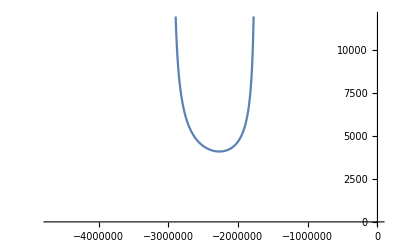

```mathematica
Plot[1/√(2*(W+1/z+f*z)),{z,zi,zb}]
```

### Downhill Bulk

```mathematica
<<ComputerArithmetic`(* Atomic to Physical Unit Conversions *)
(* 1 GHz below ZFIP in AU *)
enAU=Quantity[4.35974417*10^-18,"Joules"];
enAU1GHz=UnitConvert[Quantity["PlanckConstant"]*Quantity[1,"Gigahertz"]/enAU];
(* Print["1 GHz Photon Energy = ",enAU1GHz, " A.U."] *)
(* 1 ns in AU *)
tAU=Quantity[2.418884326505*10^-17,"Seconds"];
tAU1ns=UnitConvert[Quantity[1,"nanosecond"]/tAU];
(* Print["1 ns = ",tAU1ns, " A.U."] *)
(* 1 mV/cm in AU *)
fAU=Quantity[5.14220652*10^11,"Volts"/"Meters"];
fAU1mVcm=UnitConvert[Quantity[1,"Millivolts"/"Centimeters"]/fAU];
(* Print["1 mV/cm = ",fAU1mVcm," A.U."] *)
(* Execute *)
folder="binding_0";
(* folder="test" *)
fields=Table[i*fAU1mVcm,{i,0,300,1}];
(* fields=Table[i*fAU1mVcm,{i,0,300,50}]; *)
energies=Table[i*enAU1GHz,{i,-300,300,1}];
(* energies=Table[i*enAU1GHz,{i,-200,200,50}]; *)
Clear[f];
tidy=Function[{x},
val=x;
If[x===Indeterminate,val=NaN];
val=ToString[FortranForm[N[val]]]
];
Monitor[Do[
Clear[W,z,zi,zb,zt,t,tb,tt,results];
SetDirectory[NotebookDirectory[]];
(* Parallel Execution *)
results={};
SetSharedVariable[results];
tstart=AbsoluteTime[];
(* f=1*fAU1mVcm; *)
(* W=0*enAU1GHz; *)
zi=6;
il=-2*√f;
ParallelDo[
(* Binding *)
If[f>0&&W>il&&W<0,
zb=-W/f;
tb=NIntegrate[(1/√(2*(W+1/z+f*z))),{z,zi,zb}];
,
zb=Indeterminate;
tb=Indeterminate;
]
(* Turning *)
Which[f>0&&W<il,
zt=-1/(2*f)*(W+√(W^2-4*f));
tt=NIntegrate[(1/√(2*(W+1/z+f*z))),{z,zi,zt}];
,
f==0&&W<il,
zt=-1/W;
tt=NIntegrate[(1/√(2*(W+1/z+f*z))),{z,zi,zt}];
,
W≥il,
zt=Indeterminate;
tt=Indeterminate;]
(* Append results *)
AppendTo[results,{W,f,zb,Re[tb],Arg[tb],zt,Re[tt],Arg[tt]}]
,{W,energies}];
tend=AbsoluteTime[];
(* Export *)
fname=FileNameJoin[{folder,CreateUUID[]<>".txt"}];
header=StringJoin[
"# Filename\t"<>fname<>"\n",
"# Source\t"<>NotebookFileName[]<>"\n",
"# Note\t"<>"1D calculation of binding time vs. field and orbit energy."<>"\n",
"# Date\t"<>DateString[Now,"ISODateTime"]<>"\n",
"# Dir\t"<>"1"<>"\n",
"# field\t"<>tidy[f]<>"\n",
"# zi\t"<>tidy[zi]<>"\n",
"W"<>"\t"<>
"field"<>"\t"<>
"zb"<>"\t"<>
"tb"<>"\t"<>
"argtb"<>"\t"<>
"zt"<>"\t"<>
"tt"<>"\t"<>
"argtt"<>"\n"
];
Put[fname];
stream=OpenWrite[fname];
WriteString[stream,header]
Do[
wstring="";
Do[
wstring=StringJoin[wstring,
tidy[results[[i,j]]],"\t"];
,{j,1,Dimensions[results][[2]]}
];
wstring=StringTrim[wstring];
wstring=StringJoin[wstring,"\n"];
WriteString[stream,wstring]
,{i,1,Dimensions[results][[1]]}
];
Close[stream];
,{f,fields}],f/fAU1mVcm]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {23089.002773499725474424697255844320803452873747119156178086996079}. NIntegrate obtained 3.89699×10^6-1.85085 ⅈ and 4.14539 for the integral and error estimates.

## Scratch

```mathematica
Solve[0==1/x-α*x-β,x]
```

{{x→(-β-√(4 α+β^2))/(2 α)},{x→(-β+√(4 α+β^2))/(2 α)}}

```mathematica
Solve[0==1/x-β,x]
```

{{x→1/β}}

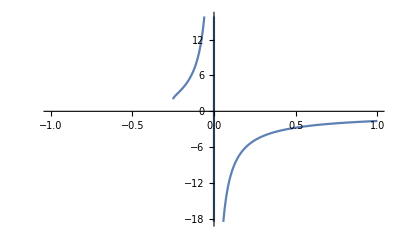

```mathematica
Plot[(-β-√(4*α+β^2))/(2*α)/.{β->1},{α,-1,1}]
```